### Mathematica Project Interactive Demonstration of Japanese Theorem Given two identical cyclic n-gons, demonstrate that no matter how one triangulates (interactive) the n-gons, the inradii of the incircles will be the constant.

## Triangle Functions

### Incenter of a Triangle Function

```mathematica
Incenter[{x1_,y1_},{x2_,y2_},{x3_,y3_}] := 
Module[{
a = EuclideanDistance[{x2,y2},{x3,y3}],
b = EuclideanDistance[{x1,y1},{x3, y3}],
c = EuclideanDistance[{x1, y1},{x2, y2}],
x, y
},

x =( a*x1+b*x2+c*x3)/(a+b+c);
y = (a*y1+b*y2+c*y3)/(a+b+c);

{x, y}


]
```

### Inradii of a Triangle Function

```mathematica
Inradius[{x1_,y1_},{x2_,y2_},{x3_,y3_}] := 
Module[{
a = EuclideanDistance[{x2,y2},{x3,y3}],
b = EuclideanDistance[{x1,y1},{x3, y3}],
c = EuclideanDistance[{x1, y1},{x2, y2}],
Area = Area[Polygon[{{x1, y1},{x2, y2}, {x3, y3}}]],
x
},
x=2*Area/(a+b+c)
]
```

```mathematica
Inradius[{0,0},{1,1},{0,1}]
```

1/(2+√2)

```mathematica
Inradius @@ exampleData (*Do apply from now on*)
```

1/(2+√2)

```mathematica
Incenter@@exampleData
```

{1/(2+√2),(1+√2)/(2+√2)}

### Visualization of a Triangle, Incenter, and Incircle

```mathematica
exampleData = {{0,0},{0,1},{1,1}};
```

```mathematica
Flatten[exampleData,0]
```

{{0,0},{0,1},{1,1}}

```mathematica
{{0,4},{0,1},{1,1}}
```

{{0,4},{0,1},{1,1}}

```mathematica
Inradius[exampleData]
```

Inradius[{{0,0},{0,1},{1,1}}]

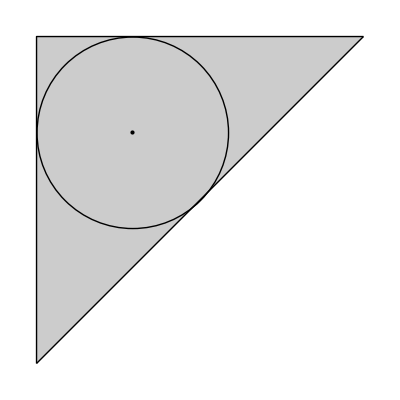

```mathematica
Graphics[
{
Opacity[.2],Polygon[{exampleData}],
Opacity[1],Black,Point[{Incenter@@exampleData}],
Black,Circle[Incenter@@exampleData,Inradius@@exampleData],
Line[{exampleData}],
Line[{Last[exampleData],First[exampleData]}]
}
]
```

## Triangulation of a Polygon

### Generation of a Regular Polygon

```mathematica
regularNGon := Graphics[Line[Table[{Cos[(i 2 π)/#],Sin[(i 2 π)/#]},{i,0,#}]]]&
```

```mathematica
tableNGon := Table[{Cos[(i 2 π)/#],Sin[(i 2 π)/#]},{i,0,#}]&
```